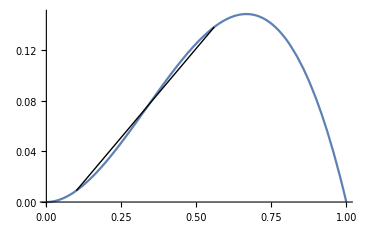

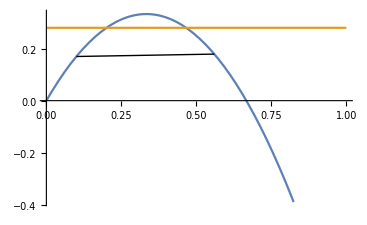

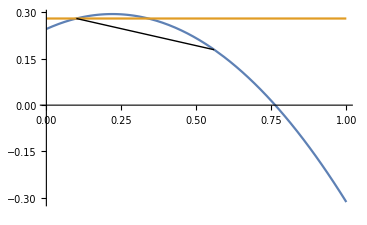

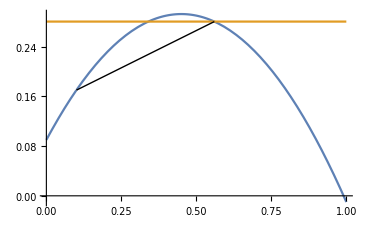

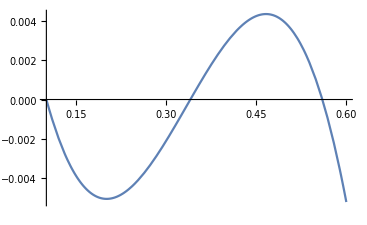

```mathematica
f[q_]:=(q^2-q^3)
qleft = 0.56;
qright = 0.1;
s[ql_,qr_]:= (f[ql]-f[qr])/(ql - qr);
Plot[f[q],{q,0,1},Epilog->{Line[{{qright,f[qright]},{qleft,f[qleft]}}]}]
Plot[{f'[q],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,f'[qright]},{qleft,f'[qleft]}}]}]
Plot[{s[q,qleft],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,s[qright,qleft]},{qleft,Limit[s[q,qleft],q->qleft]}}]}]
Plot[{s[q,qright],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,Limit[s[q,qright],q->qright]},{qleft,s[qleft,qright]}}]}]
Plot[f[q]-(s[qleft,qright]*(q - qleft)+f[qleft]),{q,qright,0.6}]
```

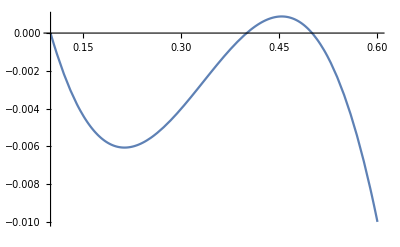

```mathematica
Plot[f[q]-(s[qleft,qright]*(q - qleft)+f[qleft]),{q,qright,0.6}]
```

```mathematica
Clear[s]
```

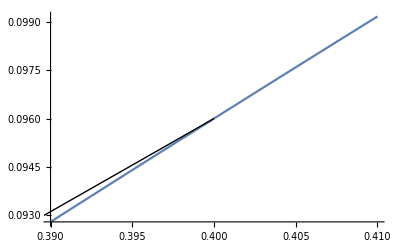

```mathematica
Plot[f[q],{q,.39,.41},Epilog->{Line[{{qright,f[qright]},{qleft,f[qleft]}}]}]
```

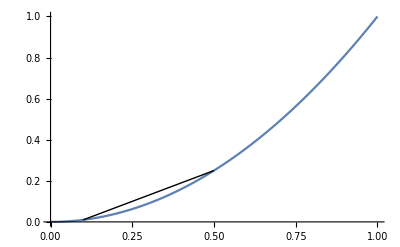

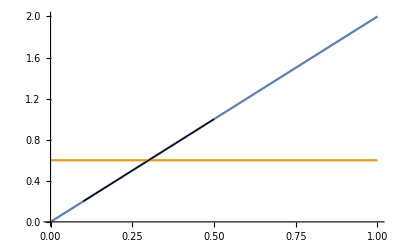

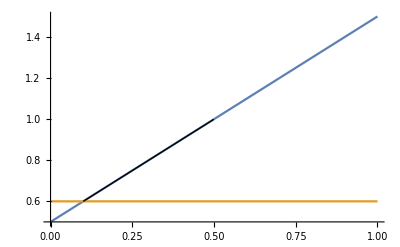

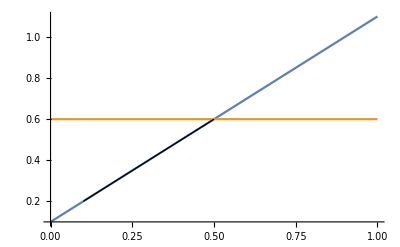

```mathematica
f[q_]:=(q^2)
qleft = 0.5;
qright = 0.1;
s[ql_,qr_]:= (f[ql]-f[qr])/(ql - qr);
Plot[f[q],{q,0,1},Epilog->{Line[{{qright,f[qright]},{qleft,f[qleft]}}]}]
Plot[{f'[q],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,f'[qright]},{qleft,f'[qleft]}}]}]
Plot[{s[q,qleft],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,s[qright,qleft]},{qleft,Limit[s[q,qleft],q->qleft]}}]}]
Plot[{s[q,qright],s[qleft,qright]},{q,0,1},Epilog->{Line[{{qright,Limit[s[q,qright],q->qright]},{qleft,s[qleft,qright]}}]}]
```

```mathematica
f[q_]:=(q^2-q^3)
qright = 0.1;
s[ql_,qr_]:= (f[ql]-f[qr])/(ql - qr);
Manipulate[Plot[f[q]-(s[qleft,qright]*(q - qleft)+f[qleft]),{q,qright,0.12}],{qleft,0.3,0.8}]
```

Plot::plln: Limiting value qright in {q,qright,0.12} is not a machine-sized real number.

Plot::plln: Limiting value qright in {q,qright,0.6} is not a machine-sized real number.

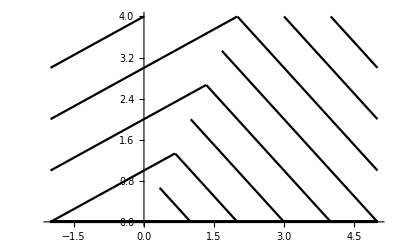

```mathematica
ul = 2;
ur = -1;
slr = (ul + ur)/2;
fl[x_,s_] := Piecewise[{{x/ul+s,x/ul+s>=x/slr && x/ul+s ≥0}},0]
fr[x_,s_] :=Piecewise[{{x/ur+s,x/ur+s<=x/slr && x/ur+s ≥0}},0] 
Show[Table[Plot[{fl[x,s],fr[x,s]},{x,-2,5},Exclusions->"Discontinuities",PlotStyle->Black,PlotRange->{0,4}],{s,-1,10,1}]]
```

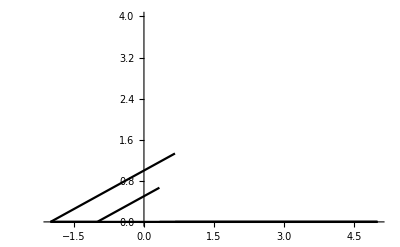

```mathematica
Show[Table[Plot[fl[x,s],{x,-2,5},Exclusions->"Discontinuities",PlotStyle->Black,PlotRange->{0,4}],{s,0,1,1/2}]]
```

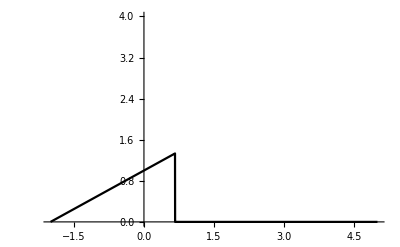

```mathematica
Plot[Flatten[Table[fl[x,1],{s,1,1,1/2}]][[1]],{x,-2,5},Exclusions->"Discontinuities",PlotStyle->Black,PlotRange->{0,4}]
```

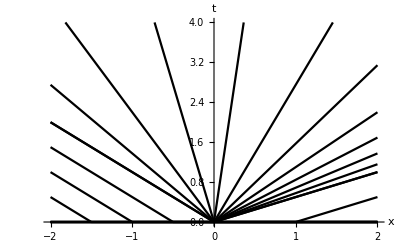

```mathematica
ul = -1;
ur = 2;
slr = (ul + ur)/2;
fl[x_,s_] := Piecewise[{{x/ul+s,x/ul+s>=x/slr && x/ul+s ≥0}},0]
fr[x_,s_] :=Piecewise[{{x/ur+s,x/ur+s<=x/slr && x/ur+s ≥0}},0] 
Plot[{Table[fl[x,s],{s,-2,0,1/2}],Table[x/c,{c,ul,ur,(ur-ul)/11}],Table[fr[x,s],{s,-2,0,1/2}]},{x,-2,2},Exclusions->True,PlotStyle->Black,PlotRange->{0,4},AxesLabel->{Style["x",Black,Medium],Style["t",Black,Medium]}]
```

```mathematica
fl[x,0]
```

Piecewise[{{2. x, 2. x≥(2 x)/(0.5+um)&&2. x≥0}, {0, True}}]

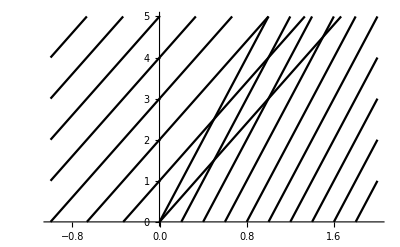

```mathematica
Plot[{Table[3x+b,{b,0,15,1}],Table[5x+b,{b,-10,0,1}]},{x,-1,2},PlotRange->{0,5},PlotStyle->Black]
```